```mathematica
(* This is necessary for removing previously defined variables *)
ClearAll["Global`*"]
```

```mathematica
findNsR[v_,vp_,ni_,nf_,ni2_,nf2_,n1guess_,plots_,prints_] := Module[{h,hsq,ϕ0,f,ϕi1,ϕpi1,ϕsol1,ϕ1p,h1sq,ϵ1,n1,ϕf2,ϕi2,ϕsol2,ϕ2p,h2sq,ϵ2,ns,r},
(* Define the hubble parameter *)
h[n_]:= Simplify[√(v[ϕ[n]]/(3-1/2*ϕ'[n]^2))];
hsq[n_]:=v[ϕ[n]]/(3-1/2*ϕ'[n]^2);
(* Find the slow roll initial conditions *)
ϕ0 = x /. Last[NSolve[vp[x]==√2*v[x],x]];
f[t_] = Integrate[v[x]/vp[x],{x,ϕ0,t}];
ϕi1= t/.Last[NSolve[ni==f[t],t]];
ϕpi1 = vp[ϕi1]/v[ϕi1] ;
(* Solve the Klein-Gordon equation for ϕ[n] *)
ϕsol1 = Last@Last@NDSolve[{2*hsq[n]*ϕ''[n]+hsq[n]*(ϕ'[n])^3-6*hsq[n]*ϕ'[n]+2*vp[ϕ[n]]==0,ϕ[ni]==ϕi1,ϕ'[ni]==ϕpi1},ϕ,{n,ni,nf},InterpolationOrder->All];
If[plots,Print[Plot[Evaluate[ϕ[n]/.ϕsol1],{n,nf,-nf},AxesLabel->{N,"ϕsol1"},GridLines->{{-1,-1.2},{1}}]]];
(* Find ϵ1 *)
ϕ1p[n_] = D[ϕ[n],n]/.ϕsol1;
h1sq[n_]:=v[ϕ[n]]/(3-1/2*ϕ1p[n]^2)/.ϕsol1;
ϵ1[n_] = Evaluate[3*ϕ1p[n]^2/(ϕ1p[n]^2+2*v[ϕ[n]]/h1sq[n])/.ϕsol1];
If[prints,Print["At n = 0",", ϵ1 = ",Evaluate[ϵ1[n]/.n->0]]];
If[plots,Print[Plot[ϵ1[n],{n,nf,ni},AxesLabel->{N,"ϵ1"},PlotRange->{{nf,-nf},{0,2}},GridLines->{{-1,-1.2},{1}}]]];
(* Solve for where ϵ1[n]==1 *)
n1 = Evaluate[n/.First[FindRoot[ϵ1[n]-1,{n,n1guess}]]];
If[prints,Print["At n1 = ",n1,", ϵ1 = ",Evaluate[ϵ1[n]/.n->n1]]];
(* Find the new initial conditions and re-solve the KG equation *)
ϕf2 = ϕ[n1]/.ϕsol1;
ϕi2 = ϕ[ni2]/.ϕsol1;
ϕsol2 = Last@Last@NDSolve[{2*hsq[n]*ϕ''[n]+hsq[n]*(ϕ'[n])^3-6*hsq[n]*ϕ'[n]+2*vp[ϕ[n]]==0,ϕ[nf2]==ϕf2,ϕ[ni2]==ϕi2},ϕ,{n,nf2,ni2},InterpolationOrder->All];
If[plots,Print[Plot[Evaluate[ϕ[n]/.ϕsol2],{n,nf2,ni2},AxesLabel->{N,"ϕsol2"}] ]];
(* Find ϵ2 *)
ϕ2p[n_] = D[ϕ[n],n]/.ϕsol2;
h2sq[n_]:=v[ϕ[n]]/(3-1/2*ϕ2p[n]^2)/.ϕsol2;
ϵ2[n_] = Evaluate[3*ϕ2p[n]^2/(ϕ2p[n]^2+2*v[ϕ[n]]/h2sq[n])/.ϕsol2];
If[prints,Print["At n = 0",", ϵ1 = ",Evaluate[ϵ2[n]/.n->0]]];
If[plots,Print[Plot[ϵ2[n],{n,nf2,ni2},AxesLabel->{N,"ϵ2"},PlotRange->{{nf2,ni2},{0,1}}]]];
(* Find the spectral tilt: ns[n] *)
ns[n_] := 1-2*ϵ2[n]+D[Log[ϵ2[n]],n];
If[prints,Print["ns[60] = ",ns[n]/.{n->60}]];
r[n_] := 16*(ϵ2[n]/.{n->60});
If[prints,Print["r[60] = ",r[n]/.{n->60}]];
If[plots,Print[Plot[Evaluate[ns[n]],{n,ni2,nf2},AxesLabel->{N,ns}]]];
(*Return[{ns[n]/.{n->60},r[n]/.{n->60}}]*)
Return[{ns[n],r[n]}]]
```

```mathematica
(* Define an inflationary potential *)
v[x_] := x^3;
vp[x_]=v'[x];
ni = 80; (* initial value f n for integration *)
nf = -1.2; (* final value of n for integration *)
ni2 = 80;
nf2 = 0;
n1guess = -1;
{ns,r} = findNsR[v,vp,ni,nf,ni2,nf2,n1guess,False,True];
Print["ns[60] = ",ns/.{n->60}," and r[60] = ",r/.{n->60}];
Print["ns[50] = ",ns/.{n->50}," and r[50] = ",r/.{n->50}];
```

At n = 0, ϵ1 = 0.438659

At n1 = -1.09074, ϵ1 = 1.

At n = 0, ϵ1 = 1.00006

ns[60] = 0.958408

r[60] = 0.199863

ns[60] = 0.958408 and r[60] = 0.199863

ns[50] = 0.950137 and r[50] = 0.199863

```mathematica
(* Loop over several monomial potentials and generate and ns vs r plot *)
ni = 80; nf = -1.2; ni2 = 80; nf2 = 0; n1guess = -1;
ns60List = {}; r60List = {}; ns50List = {}; r50List = {}; pList = {3,4,5};
Do[
Clear[v,vp,ns,r];
v[ϕ_] := ϕ^p;
vp[x_]=v'[x];
{ns,r} = findNsR[v,vp,ni,nf,ni2,nf2,n1guess,False,False];
AppendTo[ns60List,ns/.{n->60}];
AppendTo[r60List,r/.{n->60}];
AppendTo[ns50List,ns/.{n->50}];
AppendTo[r50List,r/.{n->50}];
,{p,pList}]
```

{0.958408,0.950295,0.942253}

{0.199863,0.265336,0.330245}

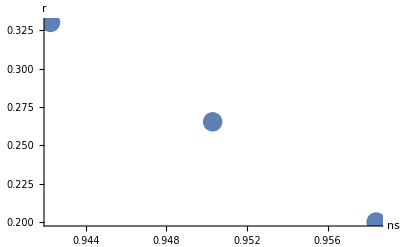

```mathematica
Print[ns60List]; Print[r60List];
ListPlot[Thread[{ns60List,r60List}],(*PlotRange->{{0.92,1},{0,0.25}},*)AxesLabel->{"ns","r"},PlotMarkers->{●,20},ColorFunction->ColorData[3,"ColorList"]]
```